```mathematica
link=Install[LinkConnect["38027@192.168.150.130,34029@192.168.150.130",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle=With[{c=4},wstpDCreateDispersionObject[c,{wstpDMaxwellianDistribution[-1,c*Sqrt[0.9],Sqrt[0.009/0.9],Sqrt[0.045/0.9]],wstpDMaxwellianDistribution[-1,c*Sqrt[0.1],Sqrt[0.1/0.1],Sqrt[0.2/0.1]],wstpDMaxwellianDistribution[1/1836,c/Sqrt[1836],0]}]];
```

{0.214735+0.00998355 ⅈ,0.275293+0.0151106 ⅈ,0.334428+0.0142621 ⅈ,0.393743+0.00954596 ⅈ,0.452656+0.00386109 ⅈ,0.509525-0.000812679 ⅈ,0.562736-0.00376705 ⅈ,0.611526-0.00514964 ⅈ,0.656356-0.00452003 ⅈ,0.695399+0.000446418 ⅈ,0.724704+0.00645198 ⅈ,0.746836+0.00936587 ⅈ,0.764726+0.00906824 ⅈ,0.779829+0.00625657 ⅈ,0.792902+0.00152999 ⅈ,0.804397-0.00467381 ⅈ,0.814617-0.0120394 ⅈ,0.823781-0.0203367 ⅈ,0.832053-0.029395 ⅈ,0.839567-0.039086 ⅈ,0.84643-0.0493117 ⅈ,0.85273-0.0599968 ⅈ,0.858543-0.0710833 ⅈ,0.863932-0.0825264 ⅈ,0.868951-0.0942918 ⅈ,0.873648-0.106354 ⅈ,0.87806-0.118696 ⅈ,0.882221-0.131303 ⅈ,0.886154-0.144169 ⅈ,0.889878-0.157287 ⅈ,0.893404-0.170652 ⅈ,0.896738-0.184258 ⅈ,0.899881-0.198094 ⅈ,0.902834-0.212147 ⅈ,0.905599-0.226402 ⅈ,0.908178-0.240837 ⅈ,0.910578-0.255435 ⅈ,0.912808-0.270176 ⅈ,0.914882-0.285043 ⅈ,0.916813-0.300024 ⅈ,0.918614-0.315107 ⅈ,0.920301-0.330287 ⅈ,0.921885-0.345558 ⅈ,0.923377-0.360916 ⅈ,0.924786-0.37636 ⅈ,0.926122-0.391889 ⅈ,0.927391-0.407501 ⅈ,0.928599-0.423197 ⅈ,0.929751-0.438974 ⅈ,0.930851-0.454834 ⅈ,0.931903-0.470776 ⅈ,0.932911-0.486798 ⅈ,0.933876-0.502901 ⅈ,0.934802-0.519083 ⅈ,0.935691-0.535345 ⅈ,0.936546-0.551685 ⅈ,0.937366-0.568102 ⅈ,0.938156-0.584597 ⅈ,0.938915-0.601167 ⅈ,0.939646-0.617813 ⅈ,0.94035-0.634533 ⅈ,0.941028-0.651326 ⅈ,0.941681-0.668193 ⅈ,0.942311-0.685131 ⅈ,0.942918-0.70214 ⅈ,0.943503-0.71922 ⅈ,0.944067-0.736369 ⅈ,0.944612-0.753587 ⅈ,0.945137-0.770873 ⅈ,0.945644-0.788226 ⅈ,0.946134-0.805645 ⅈ}

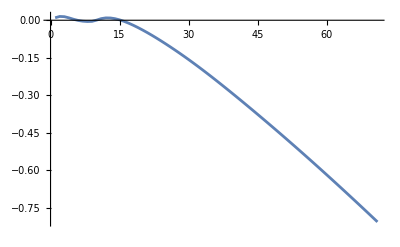

```mathematica
toright=With[{k=Range[0.5,7.5,0.1],wna=5.0Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.3,0.01] (1+0.0001 I {0,1,2}),MaxIterations->100]];
r=toright[[2,2]]
ListLinePlot[Im[r]]
```

```mathematica
toleft={};
With[{k=Range[3.0,0.5,-0.5]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.3,0.01] (1+0.0001 I {0,1,2}),MaxIterations->1000];
toleft=Append[toleft,Im[sol[[2,2]]]],{wna,5.0 Degree,25.0 Degree,1.0 Degree}]];
toright={};
With[{k=Range[3.5,7.5,0.5]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.3,0.01] (1+0.0001 I {0,1,2}),MaxIterations->1000];
toright=Append[toright,Im[sol[[2,2]]]],{wna,5.0 Degree,25.0 Degree,1.0 Degree}]];
```

```mathematica
rtoleft=Map[Reverse,toleft]
```

{{-0.0000133819,-0.000026836,-0.000040234,-0.0000535942,-0.0000669082,-0.0000801673},{-0.0000133871,-0.0000268825,-0.0000403102,-0.0000537017,-0.000067051,-0.0000803515},{-0.000013394,-0.0000269377,-0.0000404005,-0.0000538291,-0.0000672202,-0.0000805696},{-0.000013403,-0.0000270017,-0.0000405052,-0.0000539766,-0.000067416,-0.000080822},{-0.0000134144,-0.0000270746,-0.0000406243,-0.0000541444,-0.0000676387,-0.000081109},{-0.0000134287,-0.0000271566,-0.000040758,-0.0000543329,-0.0000678887,-0.000081431},{-0.0000134462,-0.0000272478,-0.0000409067,-0.0000545422,-0.0000681663,-0.0000817883},{-0.0000134674,-0.0000273484,-0.0000410705,-0.0000547726,-0.0000684718,-0.0000821815},{-0.0000134926,-0.0000274587,-0.0000412498,-0.0000550247,-0.0000688057,-0.000082611},{-0.0000135222,-0.0000275788,-0.0000414447,-0.0000552986,-0.0000691685,-0.0000830774},{-0.0000135567,-0.0000277091,-0.0000416558,-0.000055595,-0.0000695607,-0.0000835813},{-0.0000135965,-0.0000278497,-0.0000418832,-0.0000559141,-0.0000699829,-0.0000841232},{-0.0000136418,-0.000028001,-0.0000421275,-0.0000562566,-0.0000704357,-0.0000847042},{-0.0000136931,-0.0000281632,-0.000042389,-0.0000566229,-0.0000709198,-0.0000853251},{-0.0000137507,-0.0000283368,-0.0000426682,-0.0000570137,-0.0000714358,-0.0000859865},{-0.0000138149,-0.000028522,-0.0000429655,-0.0000574296,-0.0000719845,-0.0000866893},{-0.0000138861,-0.0000287192,-0.0000432816,-0.0000578712,-0.0000725671,-0.0000874346},{-0.0000139644,-0.0000289289,-0.0000436169,-0.0000583394,-0.0000731842,-0.0000882233},{-0.0000140504,-0.0000291514,-0.0000439721,-0.0000588349,-0.0000738368,-0.0000890572},{-0.0000141441,-0.0000293873,-0.0000443478,-0.0000593585,-0.0000745261,-0.0000899372},{-0.0000142459,-0.0000296369,-0.0000447447,-0.0000599112,-0.000075253,-0.0000908643}}

```mathematica
toright
```

{{-0.000093364,-0.000106492,-0.000119544,-0.000132506,-0.000145362,-0.000158091,-0.00017067,-0.00018308,-0.000195302},{-0.0000935981,-0.000106788,-0.000119915,-0.000132967,-0.000145925,-0.000158763,-0.000171455,-0.000183977,-0.000196307},{-0.0000938753,-0.000107138,-0.000120355,-0.000133513,-0.000146591,-0.000159559,-0.000172385,-0.00018504,-0.000197498},{-0.000094196,-0.000107543,-0.000120863,-0.000134144,-0.000147362,-0.00016048,-0.000173461,-0.00018627,-0.000198876},{-0.0000945605,-0.000108003,-0.00012144,-0.000134861,-0.000148237,-0.000161526,-0.000174685,-0.000187669,-0.000200442},{-0.0000949692,-0.000108518,-0.000122087,-0.000135664,-0.000149217,-0.000162699,-0.000176056,-0.000189237,-0.000202199},{-0.0000954226,-0.00010909,-0.000122803,-0.000136554,-0.000150304,-0.000164,-0.000177578,-0.000190977,-0.000204147},{-0.0000959211,-0.000109717,-0.00012359,-0.000137531,-0.000151498,-0.00016543,-0.000179251,-0.000192891,-0.00020629},{-0.0000964653,-0.000110402,-0.000124448,-0.000138595,-0.000152801,-0.00016699,-0.000181078,-0.000194981,-0.00020863},{-0.0000970556,-0.000111145,-0.000125378,-0.00013975,-0.000154212,-0.000168681,-0.000183059,-0.00019725,-0.00021117},{-0.0000976933,-0.000111946,-0.00012638,-0.000140994,-0.000155734,-0.000170506,-0.000185199,-0.000199699,-0.000213911},{-0.0000983788,-0.000112806,-0.000127456,-0.000142329,-0.000157367,-0.000172466,-0.000187497,-0.000202332,-0.000216858},{-0.0000991128,-0.000113727,-0.000128606,-0.000143755,-0.000159113,-0.000174562,-0.000189958,-0.000205151,-0.000220013},{-0.000099896,-0.000114709,-0.000129831,-0.000145274,-0.000160973,-0.000176797,-0.000192582,-0.00020816,-0.00022338},{-0.00010073,-0.000115753,-0.000131132,-0.000146887,-0.000162947,-0.000179171,-0.000195373,-0.000211361,-0.000226963},{-0.000101615,-0.000116859,-0.000132511,-0.000148594,-0.000165038,-0.000181687,-0.000198333,-0.000214758,-0.000230765},{-0.000102553,-0.00011803,-0.000133967,-0.000150397,-0.000167247,-0.000184347,-0.000201464,-0.000218354,-0.00023479},{-0.000103545,-0.000119267,-0.000135504,-0.000152298,-0.000169575,-0.000187151,-0.00020477,-0.000222153,-0.000239043},{-0.000104592,-0.00012057,-0.000137121,-0.000154297,-0.000172024,-0.000190103,-0.000208253,-0.000226158,-0.000243529},{-0.000105696,-0.000121942,-0.000138821,-0.000156396,-0.000174595,-0.000193205,-0.000211915,-0.000230374,-0.000248252},{-0.000106858,-0.000123384,-0.000140604,-0.000158596,-0.000177289,-0.000196456,-0.000215759,-0.000234804,-0.000253217}}

```mathematica
toup=Join[rtoleft,toright,2]
```

{{-0.0000133819,-0.000026836,-0.000040234,-0.0000535942,-0.0000669082,-0.0000801673,-0.000093364,-0.000106492,-0.000119544,-0.000132506,-0.000145362,-0.000158091,-0.00017067,-0.00018308,-0.000195302},{-0.0000133871,-0.0000268825,-0.0000403102,-0.0000537017,-0.000067051,-0.0000803515,-0.0000935981,-0.000106788,-0.000119915,-0.000132967,-0.000145925,-0.000158763,-0.000171455,-0.000183977,-0.000196307},{-0.000013394,-0.0000269377,-0.0000404005,-0.0000538291,-0.0000672202,-0.0000805696,-0.0000938753,-0.000107138,-0.000120355,-0.000133513,-0.000146591,-0.000159559,-0.000172385,-0.00018504,-0.000197498},{-0.000013403,-0.0000270017,-0.0000405052,-0.0000539766,-0.000067416,-0.000080822,-0.000094196,-0.000107543,-0.000120863,-0.000134144,-0.000147362,-0.00016048,-0.000173461,-0.00018627,-0.000198876},{-0.0000134144,-0.0000270746,-0.0000406243,-0.0000541444,-0.0000676387,-0.000081109,-0.0000945605,-0.000108003,-0.00012144,-0.000134861,-0.000148237,-0.000161526,-0.000174685,-0.000187669,-0.000200442},{-0.0000134287,-0.0000271566,-0.000040758,-0.0000543329,-0.0000678887,-0.000081431,-0.0000949692,-0.000108518,-0.000122087,-0.000135664,-0.000149217,-0.000162699,-0.000176056,-0.000189237,-0.000202199},{-0.0000134462,-0.0000272478,-0.0000409067,-0.0000545422,-0.0000681663,-0.0000817883,-0.0000954226,-0.00010909,-0.000122803,-0.000136554,-0.000150304,-0.000164,-0.000177578,-0.000190977,-0.000204147},{-0.0000134674,-0.0000273484,-0.0000410705,-0.0000547726,-0.0000684718,-0.0000821815,-0.0000959211,-0.000109717,-0.00012359,-0.000137531,-0.000151498,-0.00016543,-0.000179251,-0.000192891,-0.00020629},{-0.0000134926,-0.0000274587,-0.0000412498,-0.0000550247,-0.0000688057,-0.000082611,-0.0000964653,-0.000110402,-0.000124448,-0.000138595,-0.000152801,-0.00016699,-0.000181078,-0.000194981,-0.00020863},{-0.0000135222,-0.0000275788,-0.0000414447,-0.0000552986,-0.0000691685,-0.0000830774,-0.0000970556,-0.000111145,-0.000125378,-0.00013975,-0.000154212,-0.000168681,-0.000183059,-0.00019725,-0.00021117},{-0.0000135567,-0.0000277091,-0.0000416558,-0.000055595,-0.0000695607,-0.0000835813,-0.0000976933,-0.000111946,-0.00012638,-0.000140994,-0.000155734,-0.000170506,-0.000185199,-0.000199699,-0.000213911},{-0.0000135965,-0.0000278497,-0.0000418832,-0.0000559141,-0.0000699829,-0.0000841232,-0.0000983788,-0.000112806,-0.000127456,-0.000142329,-0.000157367,-0.000172466,-0.000187497,-0.000202332,-0.000216858},{-0.0000136418,-0.000028001,-0.0000421275,-0.0000562566,-0.0000704357,-0.0000847042,-0.0000991128,-0.000113727,-0.000128606,-0.000143755,-0.000159113,-0.000174562,-0.000189958,-0.000205151,-0.000220013},{-0.0000136931,-0.0000281632,-0.000042389,-0.0000566229,-0.0000709198,-0.0000853251,-0.000099896,-0.000114709,-0.000129831,-0.000145274,-0.000160973,-0.000176797,-0.000192582,-0.00020816,-0.00022338},{-0.0000137507,-0.0000283368,-0.0000426682,-0.0000570137,-0.0000714358,-0.0000859865,-0.00010073,-0.000115753,-0.000131132,-0.000146887,-0.000162947,-0.000179171,-0.000195373,-0.000211361,-0.000226963},{-0.0000138149,-0.000028522,-0.0000429655,-0.0000574296,-0.0000719845,-0.0000866893,-0.000101615,-0.000116859,-0.000132511,-0.000148594,-0.000165038,-0.000181687,-0.000198333,-0.000214758,-0.000230765},{-0.0000138861,-0.0000287192,-0.0000432816,-0.0000578712,-0.0000725671,-0.0000874346,-0.000102553,-0.00011803,-0.000133967,-0.000150397,-0.000167247,-0.000184347,-0.000201464,-0.000218354,-0.00023479},{-0.0000139644,-0.0000289289,-0.0000436169,-0.0000583394,-0.0000731842,-0.0000882233,-0.000103545,-0.000119267,-0.000135504,-0.000152298,-0.000169575,-0.000187151,-0.00020477,-0.000222153,-0.000239043},{-0.0000140504,-0.0000291514,-0.0000439721,-0.0000588349,-0.0000738368,-0.0000890572,-0.000104592,-0.00012057,-0.000137121,-0.000154297,-0.000172024,-0.000190103,-0.000208253,-0.000226158,-0.000243529},{-0.0000141441,-0.0000293873,-0.0000443478,-0.0000593585,-0.0000745261,-0.0000899372,-0.000105696,-0.000121942,-0.000138821,-0.000156396,-0.000174595,-0.000193205,-0.000211915,-0.000230374,-0.000248252},{-0.0000142459,-0.0000296369,-0.0000447447,-0.0000599112,-0.000075253,-0.0000908643,-0.000106858,-0.000123384,-0.000140604,-0.000158596,-0.000177289,-0.000196456,-0.000215759,-0.000234804,-0.000253217}}

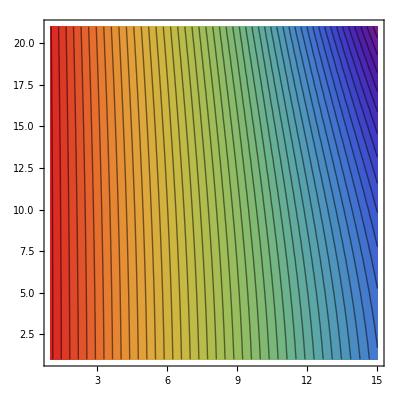

```mathematica
ListContourPlot[toup,ColorFunction->"Rainbow",Contours->50]
```